```mathematica
n=6533
```

6533

```mathematica
lst={};
```

```mathematica
Clear[tp]
lst={};
For[n=1,n≤10^6,n++,
tp=Intersection[Sign[Differences[IntegerDigits[n]]]];
If[tp=={-1,0}||tp=={0}||tp=={0,1}||tp=={1}||tp=={-1},lst=Append[lst,n]];
];
```

```mathematica
Length[lst]+8 (* Add on 1,2,3,...,9 *)
```

12951

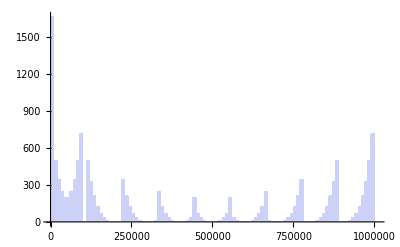

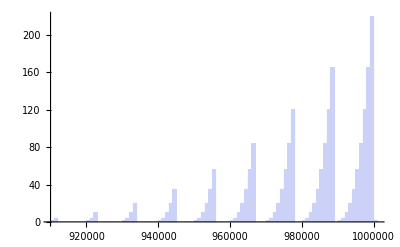

```mathematica
Histogram[lst,100]
Histogram[Select[lst,#>900000&],100]
```